Приближенные значения производной первого порядка при использовании формулы для двух узлов имеют вид: {1.9,1.85,1.75,1.6,1.45,1.35,-0.5,-1.7,-1.,-1.,-1.1}

Приближенные значения производной первого порядка при использовании формулы для трёх узлов имеют вид: {1.95,1.85,1.75,1.6,1.45,1.35,-0.5,-1.7,-1.,-1.,-1.2}

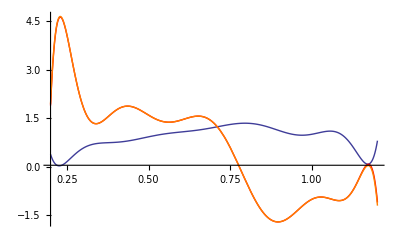

```mathematica
(*Зададим данную таблично заданную функцию*)
X={0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0,1.1,1.2};
Y={0.39,0.58,0.76,0.93,1.08,1.22,1.35,1.12,1.01,0.92,0.81};
(*Найдем количество узлов*)
n=Dimensions[X][[1]]-1;
(*Зададим шаг разбиения*)
h=0.1;
(*Построим значения производной первого порядка, используя формулы численного дифференцирования для двух узлов*)
Y12=Table[0,{j,0,n}];
(*Найдем значение производной в левом узле, используя правую рахностную производную*)
Y12[[1]]=(Y[[2]]-Y[[1]])/h;
(*Найдем значения производной во внутренних узлах, используя центральную разностную производную*)
For[j=2,j≤n,j++,
Y12[[j]]=(Y[[j+1]]-Y[[j-1]])/(2*h)
];
(*Найдем значение производной в правом узле, используя левую разностную производную*)
Y12[[n+1]]=(Y[[n]]-Y[[n+1]])/(-h);
Print["Приближенные значения производной первого порядка при использовании формулы для двух узлов имеют вид: ",Y12]
(*Построим значения производной первого порядка, используя формулы численного дифференцирования для трех узлов узлов*)
(*Значения производных для двух и трех узлов совпадают во внутренних узлах*)
Y13=Y12;
(*Найдем значение производной в левом узле*)
Y13[[1]]=(-3*Y[[1]]+4*Y[[2]]-Y[[3]])/(2*h);
(*Найдем значение производной в правом узле*)
Y13[[n+1]]=(Y[[n-1]]-4*Y[[n]]+3*Y[[n+1]])/(2*h);
Print["Приближенные значения производной первого порядка при использовании формулы для трёх узлов имеют вид: ",Y13]
(*Выполним интерполяцию функции и ее производной*)
XY=Table[{X[[j]],Y[[j]]},{j,1,n+1}];
XY12=Table[{X[[j]],Y12[[j]]},{j,1,n+1}];
XY13=Table[{X[[j]],Y13[[j]]},{j,1,n+1}];
y=InterpolatingPolynomial[XY,x];
y12=InterpolatingPolynomial[XY12,x];
y13=InterpolatingPolynomial[XY13,x];
G=Plot[y,{x,X[[1]],X[[n+1]]},PlotRange->All];
G12=Plot[y12,{x,X[[1]],X[[n+1]]},PlotStyle->Red,PlotRange->All];
G13=Plot[y13,{x,X[[1]],X[[n+1]]},PlotStyle->Orange,PlotRange->All];
Show[G,G12,G13]
```

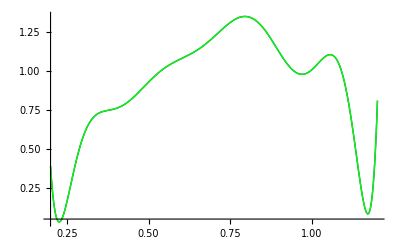

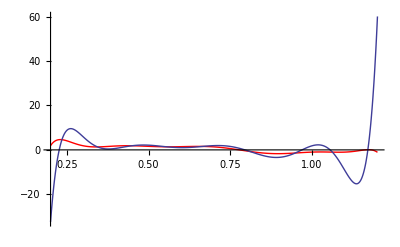

```mathematica
(*Построим многочлен Лагранжа методами XVIII века*)L[x_]=Sum[Y[[i]]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,1,i-1}]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,i+1,n+1}],{i,1,n+1}];
L1[x_]=D[L[x],x];
GL=Plot[L[x],{x,X[[1]],X[[n+1]]},PlotRange->All,PlotStyle->Green];
GL1=Plot[L1[x],{x,X[[1]],X[[n+1]]},PlotRange->All];
Show[G,GL]
Show[G12,GL1]
```